```mathematica
SetDirectory[NotebookDirectory[]];
```

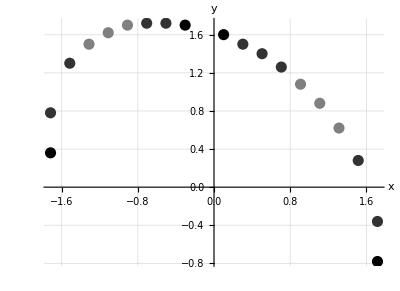

```mathematica
f1 = Import["1_10.txt","Table"];
f2  = Import["11_20.txt","Table"];
f3 = Import["21_30.txt","Table"];
f4 = Import["31_40.txt","Table"];
f5 = Import["noSol.txt","Table"];
pointSizeRed = 0.02;
pointSize= 0.02;
g1 = Graphics[{PointSize[pointSize],GrayLevel[0.8],Point[f1]}];
g2 = Graphics[{PointSize[pointSize],GrayLevel[0.5],Point[f2]}];
g3 = Graphics[{PointSize[pointSize],GrayLevel[0.2],Point[f3]}];
g4 = Graphics[{PointSize[pointSize],GrayLevel[0.005],Point[f4]}];
g5 = Graphics[{PointSize[pointSizeRed],Pink,Point[f5]}];
Show[g1,g2,g3,g4,AxesOrigin->{0,0},Axes->True,Mesh->Automatic,GridLines->Automatic,PlotRange->All,AxesStyle->Thick,AxesLabel->{"x","y"},AspectRatio->Automatic]
```